## Must Run

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5
dofs flag == 6.
*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]],
flag == 6,
filename=StringJoin["../",outputdir,"/computational_parameters.txt"]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDRho = 1+2;
IDvx = 2+2;
IDvy = 3+2;
IDtheta = 4+2;
IDsigmaxx = 5+2;
IDsigmaxy = 6+2;
IDsigmayy = 7+2;
IDqx = 8+2;
IDqy = 9+2;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = -√(2/3);
factorσ = √2;
factorq = -√(5/2);
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy}⟧ =factorq*sol⟦All,{IDqx,IDqy}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧;

trialsol
]
```

## Plotting help

### Reading the mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates*)
verts⟦All,2;;-1⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*Extract all the elements. This includes the physical groups which were defined during the mesh generation*)
Elm=mesh⟦beginElm;;-1,All⟧;

(*location where the actual quads begin, 3 because of the offset and 4 because that stores the ID of the physical entity.
The value 3 in the checks whether we have a quad or not.
*)
offset = 3;
Do[If[Length[Elm⟦ii⟧]≥5,If[Elm⟦ii⟧⟦2⟧==3,beginQuads=ii; Break[];Print["Inside"];]],{ii,1,Length[Elm]}];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-2,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh]⟦All,1;;dim⟧;
nVerts = Length[Verts];
Elms = ExtractElements[mesh];

CheckElms[Elms,nVerts];
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]},"MeshOrder"->3];

finalMesh
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData,densityValue},

(*convert data into a format which is read by Interpolation*)
densityData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];

vxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvx⟧},{ii,1,Length[solution]}];

vyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvy⟧},{ii,1,Length[solution]}];

thetaData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧},{ii,1,Length[solution]}];

(*sigmaxxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxx⟧},{ii,1,Length[solution]}];

sigmaxyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxy⟧},{ii,1,Length[solution]}];

sigmayyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmayy⟧},{ii,1,Length[solution]}];

qxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqx⟧},{ii,1,Length[solution]}];

qyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqy⟧},{ii,1,Length[solution]}];

pressureData=Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧+solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];*)

(*remove the duplicate entries for Interpolation function*)
densityData = DeleteDuplicatesBy[densityData,First];
vxData = DeleteDuplicatesBy[vxData,First];
vyData = DeleteDuplicatesBy[vyData,First];
thetaData = DeleteDuplicatesBy[thetaData,First];
(*sigmaxxData = DeleteDuplicatesBy[sigmaxxData,First];
sigmaxyData = DeleteDuplicatesBy[sigmaxyData,First];
sigmayyData = DeleteDuplicatesBy[sigmayyData,First];
qxData = DeleteDuplicatesBy[qxData,First];
qyData = DeleteDuplicatesBy[qyData,First];
pressureData=DeleteDuplicatesBy[pressureData,First];*)

(*we first need to compute the value of the solution a the mesh points*)
(*densityData=Interpolation[densityData,InterpolationOrder->1];
densityValue = densityData[0,Sequence@@#]&/@coords;*)

densityData=Interpolation[densityData,InterpolationOrder->1];
vxData=Interpolation[vxData,InterpolationOrder->1];
vyData=Interpolation[vyData,InterpolationOrder->1];
thetaData=Interpolation[thetaData,InterpolationOrder->1];
(*sigmaxxData=Interpolation[sigmaxxData,InterpolationOrder->1];
sigmaxyData=Interpolation[sigmaxyData,InterpolationOrder->1];
sigmayyData=Interpolation[sigmayyData,InterpolationOrder->1];
qxData=Interpolation[qxData,InterpolationOrder->1];
qyData=Interpolation[qyData,InterpolationOrder->1];
pressureData=Interpolation[pressureData,InterpolationOrder->1];*)

{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData}
]
```

### Plot Contour

```mathematica
PlotContour[data_,domain_,ratio_,range_]:=Module[{label},

label={Style["x",FontSize->14],Style["y",FontSize->14],None,None};

ContourPlot[data,{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],ContourLines->False,Contours->10,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/ratio,ContourLabels->False,Frame->True,FrameTicksStyle->{16,16},FrameLabel->label,RotateLabel->False,Exclusions->None]

]
```

### Plot Streamlines

```mathematica
PlotStreamlines[data_,domain_,ratio_,range_]:=Module[{},
StreamPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},PlotLegends->None,AspectRatio->1/ratio,StreamStyle->Green,StreamPoints->{Automatic,0.05},ImageSize->Large]]
```

### Plot Vector

```mathematica
PlotVectorlines[data_,domain_,ratio_,range_]:=Module[{},
VectorPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},ColorFunction->Hue,PlotLegends->Automatic,AspectRatio->1/ratio,VectorPoints->30,ImageSize->Large,VectorScale->0.05]]
```

### Sort Solution

## Solution Free Flow Channel

```mathematica
Clear[ndof]
```

### G20

```mathematica
foldername = {"Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p001_Kn0p1",
"Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p01_Kn0p1",
"Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p1_Kn0p1",
"Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_1p0_Kn0p1",
"Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_2p0_Kn0p1"};
Do[ndof[ii] = importdata[1,1,"_global_",6,foldername⟦ii⟧]⟦8,3⟧;
numsol20[ii]=importdata[ndof[ii],1,"_global_",0,foldername⟦ii⟧];
numsol20[ii] = ConvToPrim[numsol20[ii]];
solution20[ii] = InterpolateSolution[numsol20[ii]];
,{ii,1,Length[foldername]}];
```

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p001_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p001_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p01_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p01_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p1_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_0p1_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_1p0_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_1p0_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_2p0_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/output_N6_free_flow_rectangle_prescribed_Vn_2p0_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

#### vx

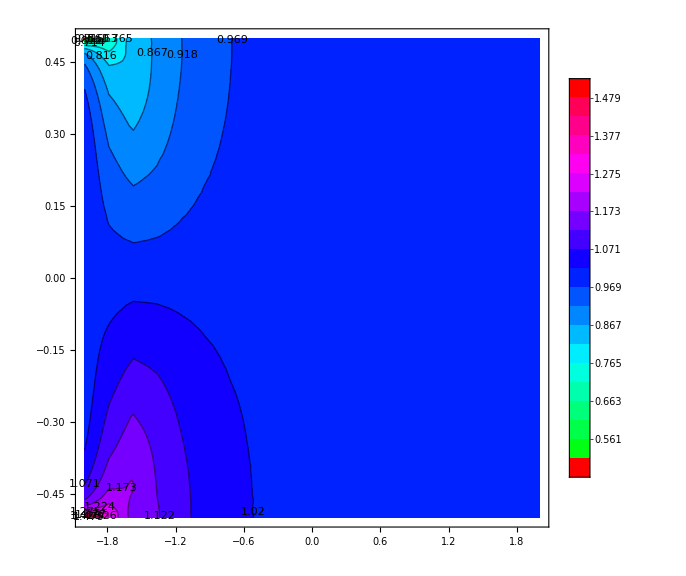

```mathematica
ContourPlot[solution20⟦IDvx-2⟧[x,y],{x,-2.0,2.0},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### vy

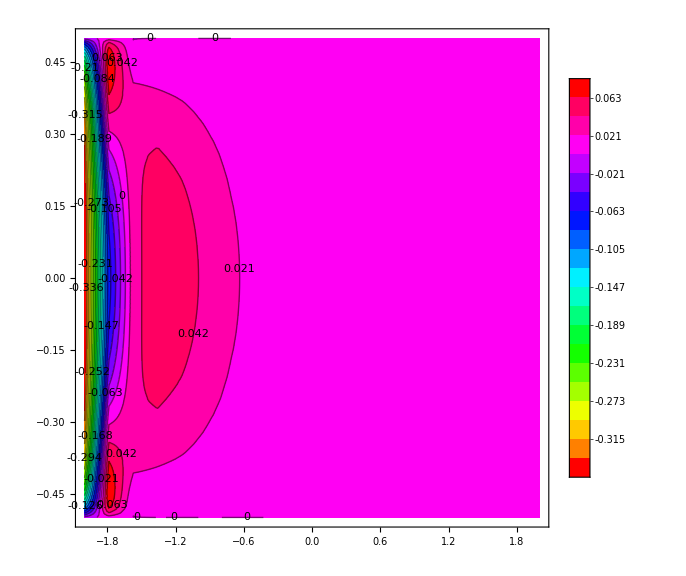

```mathematica
ContourPlot[solution20⟦IDvy-2⟧[x,y],{x,-2.0,2.0},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### θ

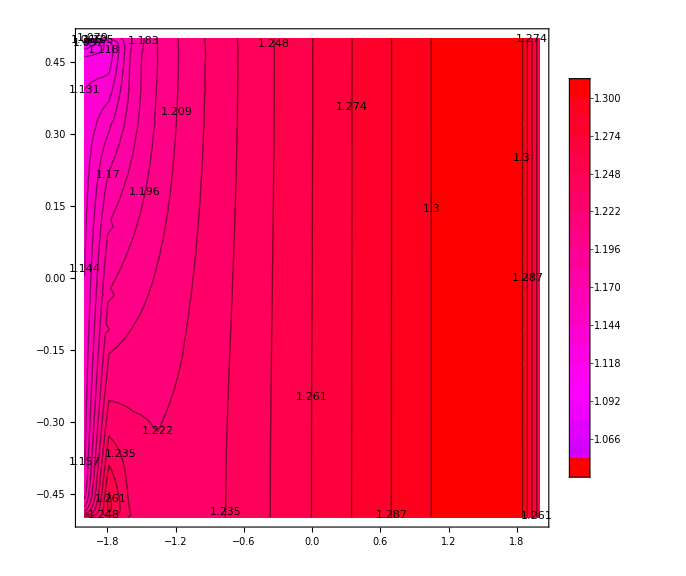

```mathematica
ContourPlot[solution20⟦IDtheta-2⟧[x,y],{x,-2,2},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### qx

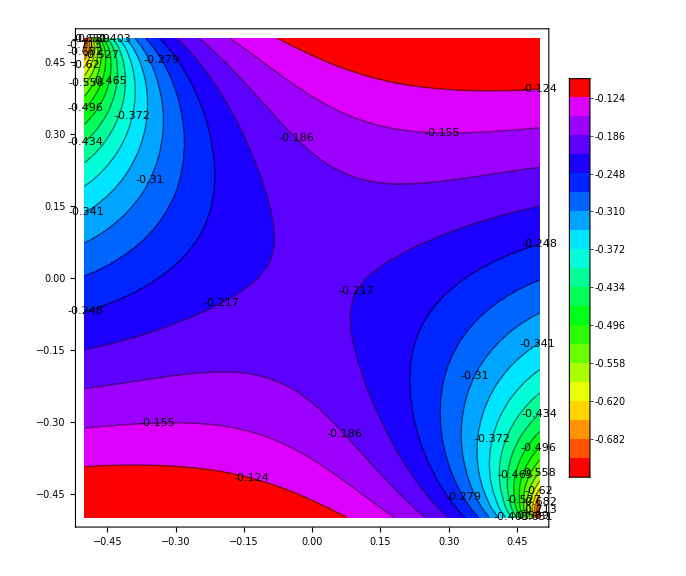

```mathematica
ContourPlot[solution20⟦IDqx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### qy

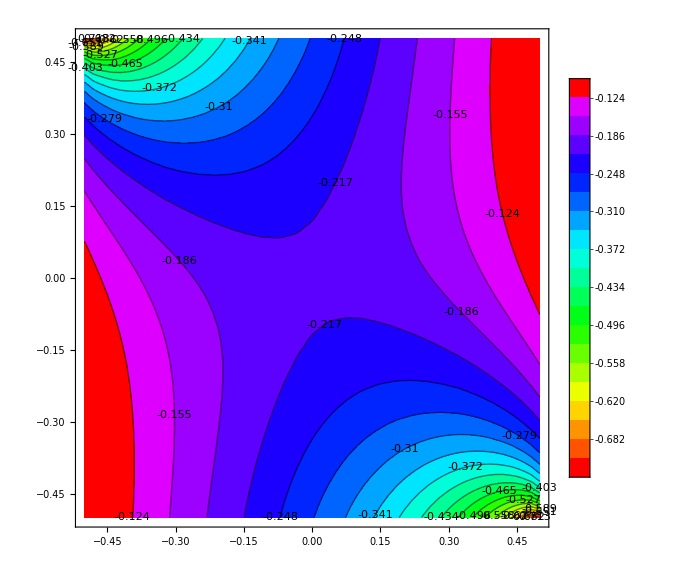

```mathematica
ContourPlot[solution20⟦IDqy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### sigmaxx

```mathematica
ContourPlot[solution20⟦IDsigmaxx-2⟧[x,y],{x,-2,2},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmaxy

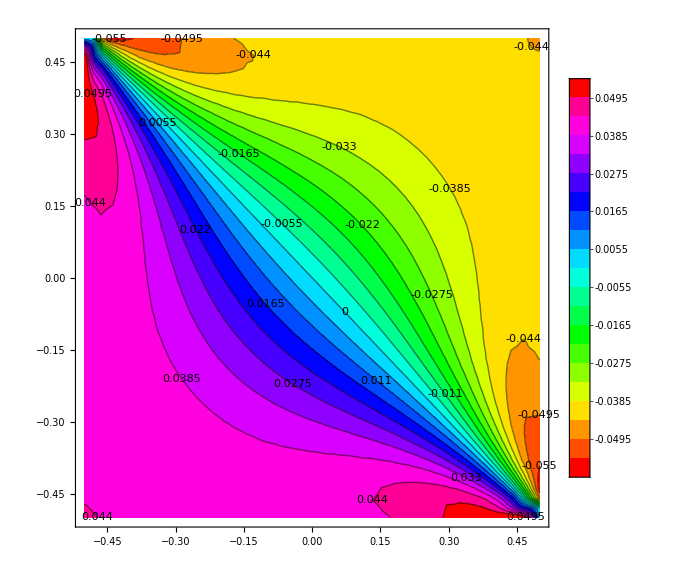

```mathematica
ContourPlot[solution20⟦IDsigmaxy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### sigmayy

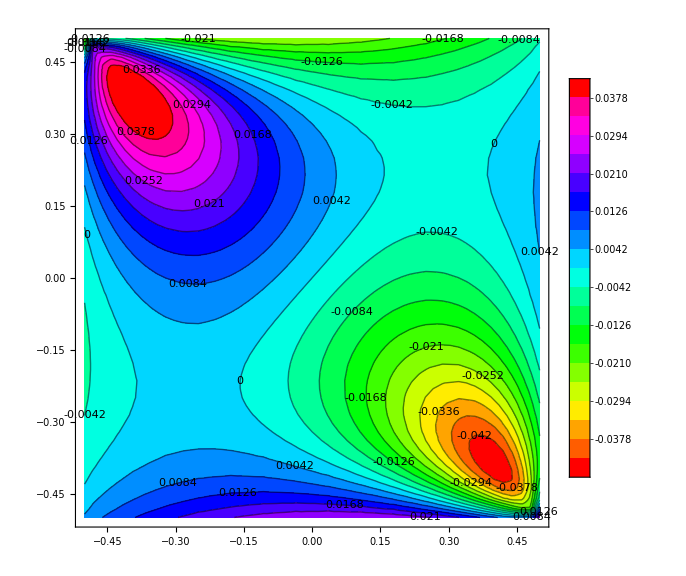

```mathematica
ContourPlot[solution20⟦IDsigmayy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

#### Velocity field

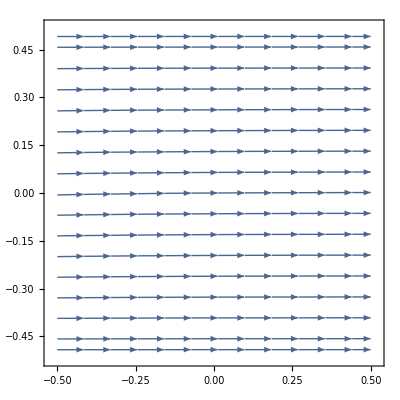

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
StreamPlot[{solution20⟦IDvx-2⟧[x,y],solution20⟦IDvy-2⟧[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,ColorFunction->Hue,AspectRatio->1]
```

#### Heat flow filed

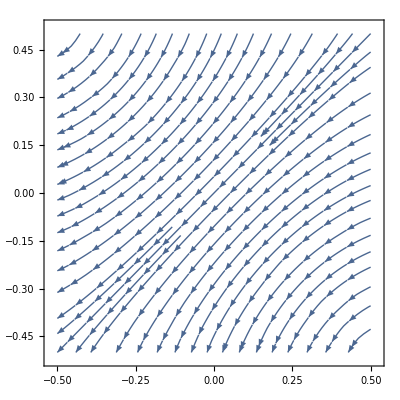

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
StreamPlot[{solution20⟦IDqx-2⟧[x,y],solution20⟦IDqy-2⟧[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,ColorFunction->Hue,AspectRatio->1]
```